```mathematica
baseq={0.025,0.032,0.04,0.047,0.062};
```

```mathematica
basep={0.1,0.13,0.16,0.19,0.25};
```

```mathematica
basenames={"Normal","Uncommon","Rare","Epic","Legendary"};
```

```mathematica
makeTicks[max_,num_]:=Table[Exp[i*Log[max]/(num-1)],{i,0,num-1}]
```

```mathematica
makePlot[baseq_,basep_,basename_]:=Module[{qr,eqns,needed,xticks,xticklabels,yticks,yticklabels,maxval,minval,barlegend},

qr=4*baseq;

eqns={1==(1+pp)*(qp*EI+qp/10*RI+qp/100*UI+qp/1000*CI+LI),
LI==1/4*(qr*EP +qr/10* RP+qr/100*UP+qr/1000*CP),
EP==(1+pp)*(qp*9/10*RI+qp/10*9/10*UI+qp/100*9/10*CI+(1-qp)*EI),
EI==1/4*(qr*9/10*RP+qr/10*9/10*UP+qr/100*9/10*CP+(1-qr)*EP),
RP==(1+pp)*(qp*9/10*UI+qp/10*9/10*CI+(1-qp)*RI),
RI==1/4*(qr*9/10*UP+qr/10*9/10*CP+(1-qr)*RP),
UP==(1+pp)*(qp*9/10*CI+(1-qp)*UI),
UI==1/4*(qr*9/10*CP+(1-qr)*UP),
CP==(1+pp)*(1-qp)*CI,
CI==1/4*(1-qr)*CP+CommonIn};
needed[q_,p_]:=CommonIn/.Solve[eqns/.{pp->p,qp->q}]⟦1⟧;

xticks=Table[N[i],{i,0,3.0,basep}];
xticklabels=Table["+"<>ToString[Round[100*xticks⟦i⟧]]<>"%",{i,1,Length[xticks]}];

yticks=Table[N[i*baseq],{i,0,8}];
maxval=N[needed[0,0]];
minval=N[needed[0,3]];
yticklabels=Table["+"<>ToString[NumberForm[100*yticks⟦i⟧,{3,1}]]<>"%",{i,1,Length[yticks]}];
(*"LabelingFunction"->(Round[#3[[1]],.1]&)*)
barlegend=BarLegend[{"Rainbow",{minval,maxval}},LabelStyle->{14,FontFamily->"Helvetica"}, LegendMarkerSize->600,LegendLabel->"Raw Ingredients Needed",Ticks->makeTicks[maxval,20],"LabelingFunction"->(NumberForm[#3[[1]],{5,1}]&)];
ContourPlot[needed[q,p],{p,0,3},{q,0,8*baseq},PlotLegends->Placed[
barlegend,Right],
Contours->35,AspectRatio->Length[yticks]/Length[xticks],ImageSize->{Automatic,640},FrameLabel->{"Total Assembler Productivity","Assembler Quality     (w/ 4 " <>basename <> " Quality Modules in Recyclers)"},FrameStyle->Directive[14,FontFamily->"Helvetica",Black],FrameTicks->{{Thread[{yticks,yticklabels}],None},{Thread[{xticks,xticklabels}],None}},GridLines->{xticks,yticks},GridLinesStyle->Directive[Dashed,White],ColorFunction->"Rainbow",PlotRange->All,ScalingFunctions->"Log",
PlotLabel->Style["Normal Raw Ingredients In per Legendary Item Out (using " <> basename <> " Modules )",24,FontFamily->"Helvetica"]
]
]
```

```mathematica
tierPlot[n_]:=makePlot[baseq[[n]],basep[[n]],basenames[[n]]]
```

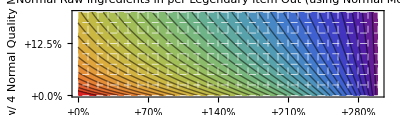

```mathematica
tierPlot[1]
```

```mathematica
Export["qualityn.png",tierPlot[1]]
Export["qualityu.png",tierPlot[2]]
Export["qualityr.png",tierPlot[3]]
Export["qualitye.png",tierPlot[4]]
Export["qualityl.png",tierPlot[5]]
```

qualityn.png

qualityu.png

qualityr.png

qualitye.png

qualityl.png